```mathematica
(*Directory[]*)
```

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\9M\\";
```

```mathematica
SetDirectory[dir1];
```

```mathematica
list=FileNames["*.jpg"];
```

```mathematica
tfinal=Length[list];
```

```mathematica
For[time=1,time<tfinal+1,time=time+1,
file=dir1<>"data"<>ToString[time]<>".jpg";
img=Import[file];
imgDRBinary=Binarize[img,1/(255)];
databn=ImageData[imgDRBinary];
(*Print[FindThreshold[img]];*)
Print[imgDRBinary];
img1=ImageMultiply[imgDRBinary,img];
{r,g,b}=ColorSeparate[img];
{w,h}=ImageDimensions[img];
data=ImageData[r,"Byte"];
datag=ImageData[g,"Byte"];
datab=ImageData[b,"Byte"];

Print[time];
(*Radius of the thermal as a function of the vertical distance, b*)
rb[time]=Total[databn,{2}]/2;
bRed[time]=Total[data,{2}];
bGreen[time]=Total[datag,{2}];
bBlue[time]=Total[datab,{2}];

ClearAll[radius];
(*Radius of the thermal as a function of the horizontal distance, a*)
Print[MemoryInUse[],"    ",MaxMemoryUsed[]];

ra[time]=Total[databn]/2;
aRed[time]=Total[data];
aGreen[time]=Total[datag];
aBlue[time]=Total[datab];

ClearAll[data,databn,datag,datab,r,g,b,img1,imgDRBinary,img,radius];

 ]
```

```mathematica
(* correction matrices *)
rbc=rb[1];
rbc[[1;;400]]=rb[tfinal][[1;;400]];
bcRed=bRed[1];
bcRed[[1;;400]]=bRed[tfinal][[1;;400]];
bcGreen=bGreen[1];
bcGreen[[1;;400]]=bGreen[tfinal][[1;;400]];
bcBlue=bBlue[1];
bcBlue[[1;;400]]=bBlue[tfinal][[1;;400]];

rac=ra[1];
acRed=aRed[1];
acGreen=aGreen[1];
acBlue=aBlue[1];
```

```mathematica
(*correcting values*)
For[time=1,time<tfinal+1,time=time+1,
rb[time]=rb[time]-rbc;
bRed[time]=bRed[time]-bcRed;
bGreen[time]=bGreen[time]-bcGreen;
bBlue[time]=Abs[bBlue[time]-bcBlue];


CbRed[time]=bRed[time]/(2*rb[time]);
CbGreen[time]=bGreen[time]/(2*rb[time]);
CbBlue[time]=bGreen[time]/(2*rb[time]);


ra[time]=ra[time]-rac;
aRed[time]=aRed[time]-acRed;
aGreen[time]=aGreen[time]-acRed;
aBlue[time]=aBlue[time]-acRed;

CaRed[time]=aRed[time]/(2*ra[time]);
CaGreen[time]=aGreen[time]/(2*ra[time]);
CaBlue[time]=aGreen[time]/(2*ra[time]);

]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

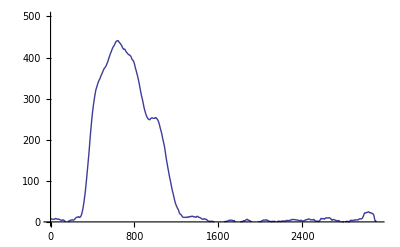
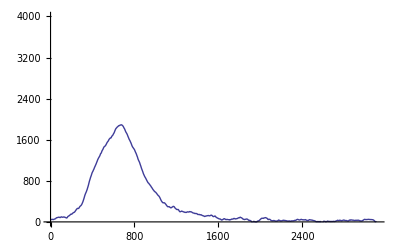
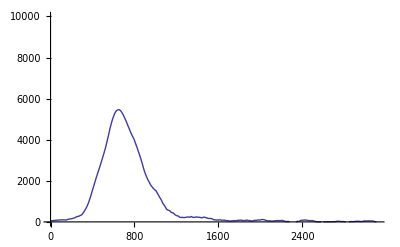
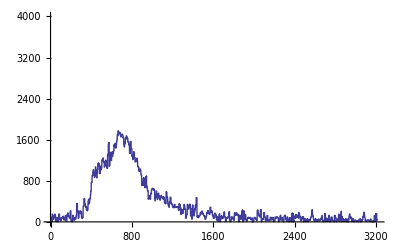
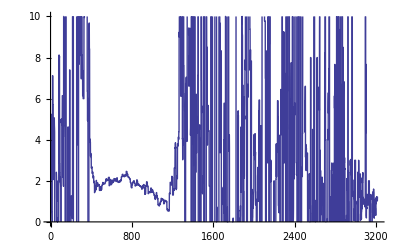
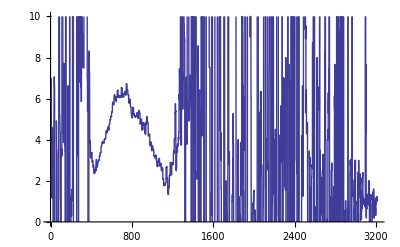
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{lr,lR,lG,lB,lCrr,lCrg,lCrb}={ListLinePlot[MovingAverage[rb[8],100],PlotRange->{0,500}],ListLinePlot[MovingAverage[bRed[8],100], PlotRange->{0,4000}],ListLinePlot[MovingAverage[bGreen[8],100], PlotRange->{0,10000}],ListLinePlot[bBlue[8], PlotRange->{0,4000}],ListLinePlot[CbRed[8], PlotRange->{0,10}],ListLinePlot[CbGreen[8], PlotRange->{0,10}],ListLinePlot[CbBlue[8], PlotRange->{0,10}]}
```

```mathematica
{lr,lR,lG,lB,lCrr,lCrg,lCrb}={Manipulate[ListPlot[rb[time],PlotRange->All, AxesLabel->{"y (pixel)","b(pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bRed[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑R)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bGreen[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑G)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bBlue[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[CbRed[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑R)_(x=1)^w/b (Bytes/pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[CbGreen[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑G/b)_(x=1)^w (Bytes/pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[CbBlue[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑B/b)_(x=1)^w (Bytes/pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}]}
```

{,,,,,,}

```mathematica
{cr,cR,cG,cB,cCrr,cCrg,cCrb}={Manipulate[ListLinePlot[ra[time],PlotRange->All, AxesLabel->{"x (pixel)","a(pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListLinePlot[aRed[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑R)_(y=1)^h (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListLinePlot[aGreen[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑G)_(y=1)^h (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListLinePlot[aBlue[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑B)_(y=1)^h (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListLinePlot[CaRed[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑R)_(y=1)^h/a (Bytes/pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListLinePlot[CaGreen[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑G)_(y=1)^h/a (Bytes/pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListLinePlot[CaBlue[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑B)_(y=1)^h/a (Bytes/pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}]}
```

{,,,,,,}

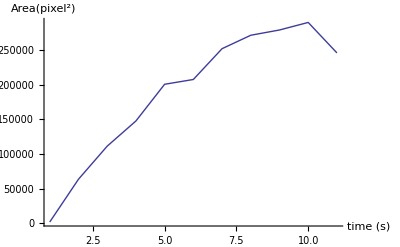
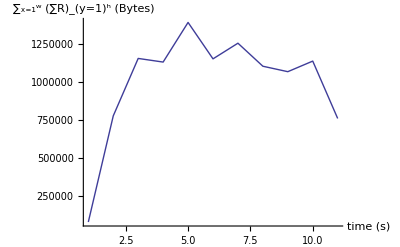
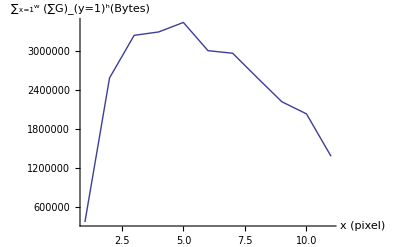
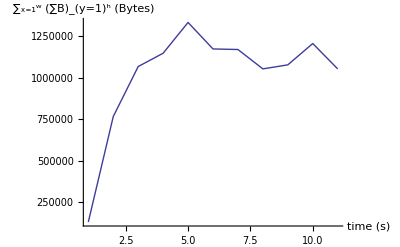
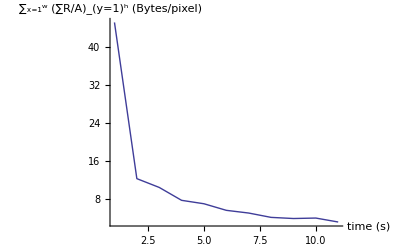
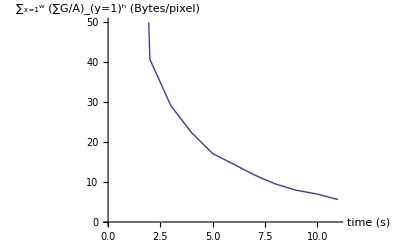
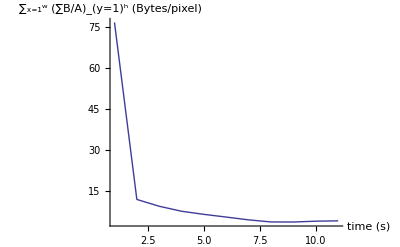

```mathematica
For[time=1, time<tfinal+1,time=time+1,
Area[time]=Total[rb[time]]*2;
TotalRed[time]=Total[bRed[time]];
TotalGreen[time]=Total[bGreen[time]];
TotalBlue[time]=Total[bBlue[time]];
Cred[time]=TotalRed[time]/Area[time];
Cgreen[time]=TotalGreen[time]/Area[time];
Cblue[time]=TotalBlue[time]/Area[time];
]

{tArea,tR,tG,tB,tCr,tCg,tCb}={ListLinePlot[Table[Area[time],{time,1,tfinal,1}],PlotRange->All, AxesLabel->{"time (s)","Area(pixel^2)"}],ListLinePlot[Table[TotalRed[time],{time,1,tfinal,1}],PlotRange->All, AxesLabel->{"time (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}],ListLinePlot[Table[TotalGreen[time],{time,1,tfinal,1}],PlotRange->All, AxesLabel->{"x (pixel)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}],ListLinePlot[Table[TotalBlue[time],{time,1,tfinal,1}],PlotRange->All, AxesLabel->{"time (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}],ListLinePlot[Table[Cred[time],{time,1,tfinal,1}],PlotRange->All, AxesLabel->{"time (s)","∑_(x=1)^w (∑R/A)_(y=1)^h (Bytes/pixel)"}],ListLinePlot[Table[Cgreen[time],{time,1,tfinal,1}],PlotRange->{0,50}, AxesLabel->{"time (s)","∑_(x=1)^w (∑G/A)_(y=1)^h (Bytes/pixel)"}],ListLinePlot[Table[Cblue[time],{time,1,tfinal,1}],PlotRange->All, AxesLabel->{"time (s)","∑_(x=1)^w (∑B/A)_(y=1)^h (Bytes/pixel)"}]}
```

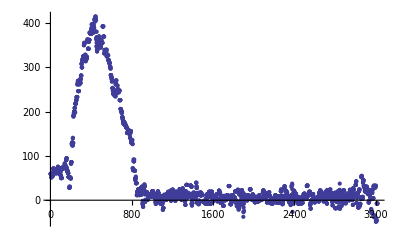

```mathematica
pdata=CbBlue[5];
ListPlot[rb[5], PlotRange->All]
```

```mathematica
pdata=rb[5]
```

{119/2,119/2,119/2,119/2,119/2,119/2,119/2,119/2,103/2,103/2,103/2,111/2,111/2,111/2,111/2,111/2,55,55,55,55,55,55,55,55,127/2,127/2,127/2,143/2,143/2,143/2,143/2,143/2,137/2,137/2,137/2,137/2,137/2,129/2,129/2,129/2,123/2,123/2,123/2,131/2,131/2,139/2,139/2,139/2,129/2,121/2,121/2,129/2,129/2,129/2,129/2,137/2,127/2,127/2,127/2,63,63,63,125/2,125/2,61,61,61,65,65,65,65,65,151/2,151/2,151/2,143/2,143/2,141/2,141/2,139/2,69,69,69,65,65,61,61,61,145/2,145/2,145/2,145/2,145/2,145/2,145/2,145/2,57,57,57,131/2,129/2,56,56,113/2,50,50,50,50,50,50,50,50,73,73,73,73,72,71,71,143/2,71,71,71,71,71,75,75,75,73,73,73,153/2,153/2,153/2,153/2,153/2,75,75,75,83,83,79,79,79,79,79,79,151/2,151/2,151/2,151/2,151/2,91,91,91,91,91,95,95,95,145/2,145/2,145/2,137/2,137/2,129/2,129/2,129/2,65,65,65,61,61,61,61,61,105/2,105/2,105/2,105/2,105/2,105/2,52,103/2,28,28,28,31,61/2,30,59/2,59/2,101/2,101/2,101/2,103/2,103/2,99/2,99/2,97/2,83,83,82,86,86,86,86,86,128,127,251/2,128,126,130,130,131,247/2,247/2,247/2,279/2,141,129,129,259/2,381/2,190,377/2,192,383/2,196,395/2,198,401/2,401/2,401/2,401/2,401/2,417/2,417/2,417/2,198,198,198,218,218,218,218,218,218,218,218,226,226,226,226,226,233,233,233,233,233,233,233,233,523/2,523/2,523/2,531/2,531/2,539/2,539/2,539/2,493/2,493/2,493/2,493/2,493/2,493/2,493/2,493/2,539/2,539/2,539/2,523/2,523/2,531/2,531/2,531/2,545/2,545/2,545/2,537/2,537/2,529/2,529/2,529/2,547/2,547/2,547/2,563/2,563/2,563/2,563/2,563/2,308,308,308,300,300,300,300,300,315,315,315,319,319,319,319,319,325,325,325,321,321,321,321,321,350,350,701/2,711/2,711/2,709/2,354,354,641/2,641/2,641/2,649/2,649/2,657/2,657/2,657/2,314,314,314,318,318,318,318,318,639/2,639/2,639/2,639/2,639/2,647/2,647/2,647/2,360,360,360,727/2,363,359,359,717/2,342,342,342,342,342,342,342,342,358,358,358,362,362,362,362,362,757/2,757/2,757/2,757/2,757/2,757/2,757/2,757/2,751/2,751/2,751/2,751/2,751/2,751/2,751/2,751/2,385,385,385,389,389,397,397,397,393,393,393,397,397,393,785/2,785/2,755/2,378,383,783/2,392,389,775/2,387,799/2,396,392,759/2,765/2,779/2,384,767/2,409,408,408,407,815/2,815/2,408,807/2,410,414,415,415,821/2,408,813/2,813/2,731/2,363,695/2,761/2,761/2,737/2,356,711/2,340,336,336,356,348,340,340,344,357,357,357,723/2,361,361,721/2,721/2,731/2,731/2,731/2,739/2,739/2,739/2,739/2,739/2,356,356,356,356,356,356,356,356,689/2,697/2,697/2,697/2,697/2,697/2,697/2,689/2,723/2,723/2,723/2,723/2,723/2,715/2,715/2,715/2,711/2,711/2,711/2,711/2,711/2,711/2,711/2,711/2,785/2,785/2,785/2,785/2,785/2,785/2,785/2,785/2,739/2,739/2,739/2,739/2,739/2,739/2,739/2,739/2,663/2,663/2,663/2,679/2,679/2,671/2,671/2,671/2,334,334,334,334,334,334,334,334,336,336,336,336,336,340,340,340,325,325,325,325,325,329,329,329,327,327,327,327,327,327,327,327,316,316,316,316,316,316,316,316,310,310,310,310,310,310,310,310,603/2,603/2,603/2,603/2,603/2,595/2,595/2,595/2,565/2,565/2,565/2,565/2,565/2,557/2,557/2,557/2,549/2,275,551/2,268,268,272,272,272,253,253,253,253,254,493/2,247,247,240,240,481/2,481/2,240,240,240,240,479/2,239,238,237,237,238,238,477/2,239,239,239,247,247,235,469/2,469/2,525/2,525/2,525/2,533/2,533/2,541/2,541/2,541/2,483/2,483/2,483/2,491/2,491/2,491/2,491/2,491/2,259,259,259,251,251,251,251,251,244,244,244,244,244,244,244,244,495/2,495/2,495/2,495/2,495/2,495/2,495/2,495/2,226,226,226,226,226,226,226,226,206,206,206,206,206,202,202,202,403/2,403/2,403/2,395/2,395/2,395/2,395/2,395/2,375/2,375/2,375/2,375/2,375/2,367/2,367/2,367/2,361/2,361/2,361/2,353/2,353/2,345/2,345/2,345/2,176,176,176,176,176,176,176,176,172,172,172,172,172,172,172,172,168,168,168,168,168,168,168,168,164,164,164,164,164,164,164,164,152,152,152,152,152,152,152,152,159,159,159,159,159,159,159,159,156,156,156,156,156,156,156,156,149,149,149,149,149,141,141,141,152,152,152,156,156,156,156,156,267/2,267/2,267/2,259/2,259/2,259/2,259/2,259/2,132,132,132,136,136,255/2,127,253/2,72,72,72,68,68,68,68,68,92,88,88,88,88,88,88,92,133/2,133/2,133/2,133/2,133/2,133/2,133/2,133/2,99/2,91/2,91/2,99/2,99/2,99/2,99/2,107/2,77/2,77/2,77/2,77/2,77/2,77/2,77/2,77/2,23/2,23/2,23/2,23/2,23/2,39/2,39/2,39/2,33/2,33/2,33/2,41/2,41/2,49/2,49/2,49/2,33/2,33/2,17,35/2,18,15,15,15,23/2,23/2,23/2,31/2,31/2,31/2,31/2,31/2,26,26,26,22,22,26,26,26,27/2,14,29/2,14,27/2,13,25/2,25/2,30,30,61/2,59/2,30,61/2,30,30,-17/2,-17/2,-5,-3/2,-2,-11,-15,-15,20,21,41/2,39/2,20,57/2,59/2,28,45/2,45/2,63/2,71/2,71/2,63/2,63/2,63/2,13,20,-7/2,-4,1,33/2,19,37/2,27/2,14,29/2,29/2,15,37/2,37/2,37/2,37/2,37/2,37/2,16,33/2,33/2,17,35/2,3/2,3/2,3/2,3/2,3/2,3/2,3/2,3/2,9,9,9,9,9,9,9,9,25/2,25/2,25/2,25/2,25/2,25/2,25/2,25/2,10,10,10,10,10,14,14,14,15/2,15/2,15/2,15/2,15/2,15/2,15/2,15/2,25/2,25/2,25/2,25/2,25/2,25/2,25/2,25/2,41/2,41/2,41/2,41/2,41/2,41/2,41/2,41/2,31/2,31/2,31/2,23/2,23/2,15/2,15/2,15/2,16,16,16,12,12,8,8,8,12,12,12,4,4,8,8,8,-9/2,-9/2,-9/2,-17/2,-17/2,-1/2,-1/2,-1/2,23/2,23/2,15/2,21/2,17/2,25/2,21/2,21/2,21/2,21/2,11,7,7,-1,3,3,20,20,20,16,16,16,16,16,-1,-1,-1,-1,-1,-3/2,-3/2,-3/2,5/2,5/2,5/2,13/2,13/2,13/2,13/2,13/2,-15/2,-15/2,-15/2,-15/2,-15/2,-7/2,-7/2,-7/2,9,9,9,9,9,9,9,9,-9/2,-9/2,-9/2,-17/2,-17/2,-9/2,-9/2,-9/2,-43/2,-43/2,-43/2,-35/2,-35/2,-35/2,-35/2,-35/2,-2,2,2,3,7/2,12,25/2,17/2,9/2,9/2,9/2,11/2,6,21/2,11,11,17/2,17/2,17/2,9/2,9/2,9/2,9/2,9/2,11/2,11/2,11/2,3/2,3/2,3/2,3/2,3/2,29/2,29/2,15,29/2,29/2,15,29/2,29/2,15,15,15,15,15,19,19,19,33/2,33/2,33/2,33/2,33/2,33/2,33/2,33/2,21/2,21/2,21/2,23/2,12,17/2,9,9,35/2,35/2,35/2,35/2,35/2,43/2,43/2,43/2,-1,-1,-1,3,3,7,7,7,41/2,41/2,41/2,33/2,33/2,25/2,25/2,25/2,24,24,24,20,20,20,20,20,23/2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,25/2,25/2,25/2,25/2,25/2,25/2,25/2,25/2,3/2,3/2,2,-3/2,-3/2,5/2,5/2,5/2,31/2,31/2,31/2,39/2,39/2,31/2,31/2,31/2,12,12,12,4,4,4,4,4,6,6,6,6,6,6,6,6,29/2,29/2,29/2,29/2,13,9,9,17/2,17,17,17,17,17,25,25,25,6,13/2,13/2,11,25/2,9,9,9,3,3,3,3,2,3/2,3/2,1,33/2,33/2,33/2,33/2,33/2,25/2,25/2,25/2,19,23,23,27,27,23,23,19,13/2,13/2,13/2,5/2,5/2,5/2,5/2,5/2,21/2,21/2,21/2,21/2,21/2,21/2,21/2,21/2,-5/2,-5/2,-5/2,-5/2,-5/2,-21/2,-21/2,-21/2,31/2,31/2,31/2,39/2,39/2,39/2,39/2,39/2,69/2,69/2,69/2,69/2,69/2,69/2,69/2,69/2,13/2,13/2,13/2,13/2,13/2,13/2,13/2,13/2,23/2,23/2,23/2,23/2,23/2,31/2,31/2,31/2,9,9,9,9,9,9,9,9,14,14,14,14,14,14,14,14,33,67/2,33,65/2,65/2,65/2,65/2,65/2,-8,17/2,30,30,31,7/2,7/2,-25/2,0,-1/2,-1,-13/2,-13/2,5/2,7,7,23/2,23/2,13,33/2,16,23/2,15/2,15/2,9,18,13/2,19/2,19/2,25/2,33/2,19/2,13/2,13/2,13/2,3,23/2,15/2,5/2,2,31/2,31/2,31/2,31/2,31/2,15/2,15/2,7,79/2,79/2,79/2,63/2,63/2,55/2,55/2,55/2,-3/2,-3/2,-3/2,-13/2,-13/2,-13/2,-13/2,-13/2,23/2,12,12,25/2,25/2,33/2,33/2,33/2,-9,-9,-9,-5,-5,-1,-1,-1,14,14,15,23/2,12,25/2,25/2,25/2,17,17,17,17,17,17,17,17,21/2,21/2,21/2,29/2,29/2,29/2,29/2,29/2,12,12,12,12,12,12,12,12,-3,-3,-3,-3,-3,-3,-3,-3,-5/2,-5/2,-5/2,-5/2,-5/2,-5/2,-5/2,-5/2,-11/2,-11/2,-11/2,-11/2,-11/2,-11/2,-11/2,-11/2,1/2,-15/2,-15/2,-15/2,-15/2,-7/2,-7/2,9/2,-5,-5,-9/2,1/2,1/2,-1/2,-1,-1,10,10,10,10,10,14,14,14,-8,-8,-8,-4,-4,-4,-4,-4,15/2,15/2,15/2,15/2,15/2,15/2,15/2,15/2,19,19,19,19,19,19,19,19,-4,-4,-4,-8,-8,-8,-8,-8,7,7,7,7,7,11,11,11,39/2,39/2,39/2,31/2,31/2,23/2,23/2,23/2,-4,-4,-4,0,0,0,0,0,5,5,5,5,5,5,5,5,9/2,9/2,9/2,9/2,9/2,17/2,17/2,17/2,15/2,15/2,15/2,15/2,15/2,15/2,15/2,15/2,6,6,6,6,6,6,6,6,13,13,13,13,13,13,13,13,-5/2,-5/2,-5/2,3/2,3/2,3/2,3/2,3/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,43/2,43/2,43/2,43/2,43/2,35/2,35/2,35/2,16,16,16,16,16,12,12,12,-6,-6,-6,-2,-2,-2,-2,-2,-4,-4,-4,-4,-4,-4,-4,-4,9/2,9/2,9/2,9/2,9/2,9/2,9/2,9/2,-25/2,-25/2,-25/2,-25/2,-25/2,-25/2,-25/2,-25/2,19/2,19/2,19/2,19/2,19/2,19/2,19/2,19/2,0,0,0,0,0,0,0,0,15/2,15/2,15/2,15/2,15/2,15/2,15/2,15/2,6,6,6,2,2,2,2,2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,17/2,17/2,17/2,17/2,17/2,17/2,17/2,17/2,32,32,32,32,32,32,32,32,3,3,3,7,7,7,7,7,-9,-9,-9,-9,-9,-9,-9,-9,-1/2,-1/2,-1/2,-1/2,-1/2,-9/2,-9/2,-9/2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,17/2,17/2,17/2,17/2,17/2,17/2,17/2,17/2,2,2,2,2,2,2,2,2,6,6,6,6,6,2,2,2,20,20,20,20,20,20,20,20,-1/2,-1/2,-1/2,-9/2,-9/2,-17/2,-17/2,-17/2,-27/2,-27/2,-19/2,-11/2,-11/2,-19/2,-19/2,-19/2,18,24,20,43/2,20,20,22,47/2,-33/2,-41/2,-43/2,-35/2,-14,-16,-33/2,-18,13,13,13,17,17,17,17,17,-21/2,-21/2,-7,-1,-3/2,-11/2,-11/2,-11/2,21/2,25/2,11,17/2,17/2,2,0,0,45/2,45/2,22,45/2,22,18,18,18,12,-19/2,-11,19/2,1/2,11/2,9/2,4,-75/2,-26,-27,-33/2,21/2,15,-8,-24,2,5/2,3,7/2,4,0,-1,-1,19/2,19/2,19/2,19/2,19/2,19/2,19/2,19/2,3/2,3/2,3/2,3/2,3/2,3/2,3/2,3/2,15/2,15/2,15/2,7/2,7/2,-1/2,-1/2,-1/2,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,4,4,4,4,4,8,8,8,49/2,49/2,49/2,49/2,49/2,49/2,49/2,49/2,6,6,6,6,6,2,2,2,13/2,13/2,13/2,13/2,13/2,5/2,5/2,5/2,9,9,9,13,13,13,13,13,2,2,2,1,1/2,4,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,-9/2,-9/2,-9/2,-9/2,-9/2,-9/2,-9/2,-9/2,15/2,15/2,15/2,7/2,7/2,15/2,15/2,15/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,-7/2,-7/2,-7/2,-7/2,-7/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,15/2,15/2,15/2,15/2,15/2,23/2,23/2,23/2,0,0,0,0,0,0,0,0,3,3,3,4,9/2,9/2,9/2,9/2,11/2,11/2,11/2,3/2,3/2,3/2,3/2,3/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,18,18,18,22,22,22,22,22,17/2,17/2,17/2,17/2,17/2,25/2,25/2,25/2,11/2,11/2,11/2,11/2,11/2,11/2,11/2,11/2,15/2,15/2,15/2,15/2,15/2,7/2,7/2,7/2,31/2,31/2,31/2,31/2,31/2,31/2,31/2,31/2,-5,-5,-5,-5,-5,-1,-1,-1,12,12,12,12,12,12,12,12,14,14,14,14,14,18,18,18,10,10,10,10,10,10,10,10,-13/2,-13/2,-13/2,-13/2,-13/2,-13/2,-13/2,-13/2,3,3,3,3,3,-1,-1,-1,-4,-4,-4,-4,-4,-8,-8,-8,4,4,4,0,0,0,0,0,2,2,2,2,2,2,2,2,-3,-3,-3,-3,-3,-3,-3,-3,11,11,11,11,11,11,11,11,-5,-5,-5,-1,-1,-1,-1,-1,-3,-3,-3,-3,-3,1,1,1,9,9,9,9,9,9,9,9,-6,-6,-6,-6,-6,-6,-6,-6,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,19/2,19/2,19/2,11/2,11/2,19/2,19/2,19/2,41/2,41/2,41/2,49/2,24,20,20,39/2,-4,-4,-4,-4,-4,1,1,1,-9,-9,-9,-17/2,-8,-7/2,-7/2,-7/2,15/2,15/2,19/2,13/2,13/2,19/2,15/2,15/2,55/2,55/2,55/2,55/2,55/2,63/2,63/2,63/2,3,3,3,3,3,7,7,7,21,21,21,21,21,21,21,21,17,17,17,17,17,17,17,17,10,10,10,10,10,6,6,6,3/2,1,5,17/2,17/2,5,5,11/2,-7/2,-3,-1,-2,-3/2,-11/2,-11/2,-4,1/2,15/2,5/2,5,13/2,-1/2,1,5/2,1,-11,-21/2,4,3,11,10,9,7,65/2,59/2,-1/2,-5,3,23/2,12,75/2,69/2,49/2,-7,-53/2,27/2,14,3/2,1/2,1/2,9/2,2,13/2,8,-8,-7/2,21,22,21,41/2,41/2,39/2,39/2,37/2,-1,-1,-1,-1/2,-1/2,4,4,4,14,14,14,14,14,14,14,14,17/2,17/2,17/2,17/2,17/2,17/2,17/2,17/2,-2,-2,-2,-2,-2,-2,-2,-2,-9/2,-9/2,-9/2,-9/2,-9/2,-17/2,-17/2,-17/2,7,7,7,7,7,3,3,3,-1,-1,-1,-1,-1,-5,-5,-5,-2,-2,-2,-2,-2,-2,-2,-2,-15/2,-15/2,-15/2,-15/2,-15/2,-7/2,-7/2,-7/2,-2,-2,-2,-2,-2,-6,-6,-6,7,7,7,7,7,13/2,6,6,13,13,13,13,27/2,14,14,14,15,15,15,7,7,7,7,7,13/2,13/2,13/2,13/2,13/2,13/2,13/2,13/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,32,32,32,65/2,67/2,33,33,67/2,21/2,21/2,21/2,21/2,21/2,21/2,21/2,21/2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,23/2,19,19,19,19,19,19,19,19,-11,-11,-11,-7,-7,-19,-19,-19,-1,-1,-1,-1,-1,-1,-1,-1,-5,-5,-5,-1,-1,-1,-1,-1,10,10,10,10,10,14,14,14,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,-7/2,-3,-2,-2,-2,-5,-5,-5,7/2,7/2,7/2,7/2,7/2,7/2,7/2,7/2,5/2,5/2,5/2,5/2,3,7/2,7/2,7/2,6,6,6,6,6,6,6,6,13/2,13/2,13/2,13/2,13/2,5/2,5/2,5/2,1,1,1,1,1,-3,-3,-3,33/2,33/2,33/2,25/2,25/2,9/2,9/2,9/2,29/2,29/2,37/2,45/2,45/2,21/2,21/2,21/2,15,15,17,21,19,12,23/2,21/2,29/2,29/2,29/2,13/2,13/2,15,14,15,7,7,13/2,15/2,8,5,13/2,13/2,7/2,4,9/2,2,3,-2,-3,-3,7,7,7,3,3/2,11/2,11/2,5,14,14,14,14,14,14,14,14,19,19,18,27/2,27/2,16,16,16,0,1/2,1/2,1,1,-15/2,-15/2,-8,45/2,45/2,45/2,45/2,45/2,37/2,37/2,37/2,11,21/2,21/2,21/2,21/2,21/2,21/2,21/2,9/2,9/2,9/2,9/2,9/2,17/2,17/2,17/2,19,19,19,39/2,39/2,24,49/2,49/2,18,18,18,18,18,14,14,14,23/2,23/2,23/2,23/2,23/2,31/2,31/2,31/2,-7/2,-7/2,-7/2,-7/2,-7/2,-23/2,-23/2,-23/2,2,2,2,2,2,6,6,6,10,10,10,10,10,10,10,10,13,14,13,27/2,25/2,17,33/2,17,-18,-18,-18,-18,-18,-18,-18,-18,-7/2,1/2,1/2,1/2,1/2,1/2,1/2,-7/2,8,8,8,8,8,4,4,4,37/2,18,37/2,31/2,16,41/2,41/2,21,-5,-17,-35/2,-27/2,-37/2,7/2,2,1/2,13,25/2,43/2,47/2,75/2,21/2,9/2,-39/2,7/2,4,7/2,-3/2,3,15,35/2,41/2,4,8,15/2,9,9,17/2,-27/2,11/2,8,-5,-5,9/2,-2,1,-2,-9,12,12,23/2,23/2,21/2,45/2,31/2,31/2,-1/2,-1/2,0,3,2,22,45/2,22,6,6,6,6,6,2,2,2,-3,-3,-3,-3,-3,-7,-7,-7,8,4,4,8,8,4,4,8,0,1/2,1/2,1,3/2,29/2,15,15,19/2,9,6,3,5/2,7/2,11/2,19/2,23/2,23/2,23/2,21/2,19/2,3/2,3/2,2,-1/2,-1/2,0,1/2,1,6,6,6,47/2,47/2,47/2,39/2,39/2,39/2,39/2,39/2,10,10,10,14,14,14,14,14,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,3/2,3/2,3/2,3/2,3/2,-21/2,-21/2,-21/2,53/2,27,55/2,47/2,47/2,47/2,23,45/2,10,10,10,10,10,14,14,14,15/2,15/2,15/2,15/2,15/2,15/2,15/2,15/2,69/2,69/2,69/2,69/2,69/2,85/2,85/2,85/2,-13/2,-13/2,-13/2,-13/2,-13/2,11/2,11/2,11/2,31/2,31/2,31/2,31/2,31/2,31/2,31/2,31/2,-31/2,-33/2,-33/2,-29/2,-29/2,-15,-31/2,-17,20,20,20,24,24,24,24,24,-13,-13,-25/2,-11,-10,-17/2,-8,-8,7,7,7,7,7,3,4,9/2,52,52,54,55,55,54,52,52,7/2,7/2,7/2,7/2,7/2,15/2,15/2,15/2,79/2,79/2,40,45,45,44,89/2,91/2,65/2,65/2,63/2,63/2,61/2,59/2,61/2,31,28,57/2,55/2,41/2,20,47/2,45/2,22,31,31,31,19,18,23,24,24,53/2,53/2,53/2,53/2,53/2,61/2,61/2,61/2,25,25,25,25,25,25,25,25,29/2,29/2,29/2,29/2,29/2,29/2,29/2,29/2,-5,-5,-5,-5,-5,-1,-1,-1,23/2,23/2,12,13,13,8,15/2,15/2,35/2,35/2,35/2,43/2,43/2,43/2,43/2,43/2,-41/2,-41/2,-41/2,-49/2,-49/2,-57/2,-57/2,-57/2,33/2,33/2,33/2,33/2,17,45/2,23,23,9/2,9/2,9/2,9/2,9/2,9/2,9/2,9/2,31,30,30,33,33,29,29,29,-77/2,-77/2,-77/2,-69/2,-69/2,-77/2,-77/2,-77/2,57/2,57/2,57/2,65/2,65/2,65/2,65/2,65/2,-49,-95/2,-93/2,-45,-87/2,-87/2,-46,-95/2,-15/2,-15/2,-15/2,-15/2,-15/2,-15/2,-15/2,-15/2}

```mathematica
Abs[Fourier[pdata]]
```

{3534.03,2965.95,2370.65,1733.59,1101.73,562.146,237.741,200.646,206.856,190.081,194.347,100.683,59.7221,140.868,191.82,135.346,67.083,138.265,85.9695,86.7146,21.3893,37.2562,11.3726,54.6383,125.247,119.824,103.877,19.3323,72.0296,52.8029,70.5765,69.5206,54.0593,34.3263,96.8777,65.1486,71.6395,63.6759,25.3219,47.9477,34.8988,37.5485,9.5909,44.6554,29.8198,74.7969,62.4738,36.4576,7.46461,21.4913,32.4247,17.5785,36.8613,45.7129,26.4422,35.2056,19.9167,27.8116,32.7493,38.3272,26.5106,40.4948,23.7956,38.7849,24.7537,12.3221,20.2688,6.46725,12.3276,18.3616,39.0069,25.4129,8.29897,17.1648,41.1294,37.9707,2.04768,17.1997,44.0322,15.5217,33.5917,47.3715,30.9001,45.2333,16.3894,20.4733,15.4385,30.7704,12.4,35.0989,41.6835,2.60679,11.8527,40.3978,28.1321,9.08566,25.1938,37.0553,3.35738,11.6439,35.46,26.5557,34.7964,24.2266,16.024,28.9894,32.2793,14.673,21.8201,16.5122,46.8626,16.362,20.9377,32.7144,26.7461,17.808,17.8088,35.8955,42.8754,31.9039,39.3945,6.09991,18.3819,18.779,36.5333,24.1358,53.2146,44.4303,31.9049,7.85005,31.7438,22.4705,13.8301,22.258,12.1413,18.5768,23.7948,27.9846,32.8601,13.3023,29.4596,20.2727,23.5167,29.0296,41.5625,23.4051,13.7754,24.145,14.4906,12.4982,14.7401,24.9491,10.3913,10.8292,10.0972,27.5835,24.6576,37.5734,12.2174,14.7983,4.41209,45.7496,29.811,9.84967,55.0577,14.0029,27.5205,28.521,38.2088,19.5482,14.0306,13.2879,9.52075,8.75097,29.6467,16.6096,26.1698,27.8579,6.41712,34.0577,36.9697,23.4783,32.1944,41.055,20.733,27.1664,5.49473,5.02683,21.1111,12.5488,24.823,7.37924,38.3459,13.5434,15.1592,8.23754,12.4957,20.7147,14.2746,31.2664,29.9,22.5444,29.5526,20.2982,13.917,7.46003,9.44003,8.90528,14.1059,23.4706,38.4439,10.3691,17.0206,21.4568,13.1159,13.5354,10.3655,29.7836,31.2103,45.3497,25.3953,17.4297,30.0479,15.3813,7.41982,19.6178,22.9172,13.4953,18.202,8.86865,13.1626,8.70135,6.80029,11.555,26.31,15.4413,18.5043,10.7372,37.8234,5.25136,18.537,30.72,3.24243,3.90543,11.2445,27.6159,27.3456,15.314,2.36911,10.6325,13.5819,11.6476,14.3656,8.1222,6.06136,17.168,6.28619,13.7845,18.922,8.9198,7.87957,15.2954,12.7913,12.1883,15.2777,16.9854,14.1754,13.3323,7.73362,7.92693,10.3093,5.91343,16.6765,6.97508,14.6039,28.1023,21.4324,10.0735,18.2379,15.8517,8.17181,6.64897,17.549,16.4304,20.5655,14.863,9.29539,2.64551,9.40649,11.8815,18.1262,12.894,17.4191,12.5294,1.57325,3.98654,23.1328,13.7747,3.45046,14.7895,7.31505,14.007,11.7814,1.3558,6.42949,12.9346,11.1391,4.97966,11.7776,9.36623,3.71624,3.14937,9.80412,9.90356,2.90016,7.74752,10.9812,8.36338,1.29522,12.6005,15.0411,15.1077,8.03134,4.45237,9.45446,7.56559,9.94317,7.03629,10.6945,2.5948,3.52689,8.21724,15.23,9.65204,5.05309,6.16288,3.2846,5.99244,9.19141,8.34569,8.15416,4.16209,4.79773,4.8888,12.5697,4.8327,4.43731,5.63371,10.4049,6.83994,10.2705,9.08345,11.1416,8.36344,10.1514,7.21956,6.1258,10.4439,9.53613,10.9991,3.55076,3.22931,3.76909,7.67841,6.83136,6.95394,0.611264,4.48016,10.9749,10.2979,6.05568,9.01573,0.923074,10.9922,11.2463,3.55954,3.21033,5.81744,7.76492,5.81708,6.97786,2.12795,4.11113,2.85316,0.890416,1.66853,6.74982,1.92198,3.61578,3.97483,5.26082,7.76886,4.10428,10.2287,3.24596,8.23251,2.61583,4.49722,11.8084,18.1506,10.1148,8.27758,5.99435,6.2862,4.3184,9.653,5.88357,5.60662,1.62701,2.46075,7.51507,6.02162,6.71604,4.44511,2.2214,9.37004,3.71485,3.65885,1.21254,5.05376,6.08646,1.17182,0.618431,5.40613,6.89823,2.50762,11.4657,10.3301,4.7352,2.32434,7.02018,1.55318,4.02974,12.2082,4.40701,4.51986,8.7053,5.04868,6.85458,12.804,2.82893,2.61625,3.68799,5.68113,1.40694,6.08307,2.35181,13.2064,6.22675,3.42182,3.31936,7.08157,5.30854,2.00914,10.0831,7.38296,6.17835,1.89569,1.26683,7.73988,11.3299,5.66823,7.5841,2.92736,6.76613,4.45325,7.78165,1.31524,7.19366,2.32536,3.81875,3.43637,6.80476,9.77635,5.2018,4.40561,10.2454,9.0654,1.93649,0.546205,13.2436,4.81131,10.5967,11.4392,11.292,12.9221,6.00058,5.53949,9.92102,8.02605,3.09358,7.10692,8.8492,7.34619,2.0987,14.3864,9.50349,4.09618,6.92639,7.47762,6.10334,7.29252,11.1353,5.42683,11.8159,10.8644,3.46147,2.12964,11.4567,1.9911,6.3748,10.7321,9.10115,6.54925,6.32037,11.0024,8.69693,9.35299,3.78433,7.1057,13.2317,3.5032,8.9489,2.5872,4.22992,10.4605,15.4378,6.40482,15.5033,10.7143,6.49815,1.28962,11.9234,2.09466,6.55154,6.02278,6.00226,5.70961,4.56782,5.88359,13.967,5.28525,10.122,6.10153,7.22413,6.83422,6.47271,10.3644,3.51784,3.47684,1.11097,2.2752,11.946,6.18848,1.89026,5.08711,9.7139,7.70148,14.6179,16.4282,0.701607,3.32746,5.76743,13.8442,9.95053,7.74659,13.9383,10.0487,12.8144,4.79188,14.1308,8.37741,5.4972,5.4153,2.62399,6.43984,15.1059,9.47611,14.7975,8.09605,5.83475,12.0807,17.6041,4.31849,12.3731,11.4126,7.50952,12.4739,7.69723,4.63961,7.83247,4.28406,4.23841,4.45874,11.2388,13.3646,4.01779,5.93462,7.67904,3.88808,7.76282,6.92921,14.3172,0.470904,10.3753,9.26778,7.7991,7.54673,8.58124,9.34031,4.77503,9.10889,9.74746,4.25749,6.42694,1.21254,7.81879,3.66726,5.72441,10.4438,4.64499,10.3825,13.3534,3.90326,11.0824,12.9208,4.52585,7.82117,13.0015,8.37254,12.6426,6.24093,3.22737,4.82781,3.31854,8.14851,12.5305,6.13073,10.1288,6.74551,13.4015,3.8501,8.61696,11.4285,3.19074,4.81381,2.59043,12.4592,12.4761,5.79637,6.3543,3.92908,2.35266,5.34234,7.48363,4.01587,0.694726,6.07783,6.83145,5.07069,6.66062,2.29148,7.54928,6.06895,9.91789,2.17526,8.73956,5.02442,1.40522,3.5675,3.56428,3.14769,3.25933,5.63916,8.02579,3.02549,7.40593,8.24219,10.6338,6.7057,9.88603,7.8869,2.23366,2.16318,9.26335,5.06783,7.16673,6.60069,3.64894,5.17113,6.76542,6.70499,5.87949,2.30163,8.60405,7.59434,6.15656,0.704996,9.73289,6.08166,2.27419,5.83476,8.88333,2.9818,7.78422,1.03749,0.851765,4.11495,5.47252,1.69554,4.69368,7.57061,5.37369,2.30624,7.97125,3.53563,3.32635,4.02132,3.19079,1.53115,4.98273,10.0947,4.26854,8.53588,5.04918,2.98304,8.49457,2.31882,4.2431,4.65443,4.33343,1.27449,1.58636,5.53897,3.14017,4.50387,1.2361,1.85051,0.639586,1.49399,3.76035,4.6405,0.794817,4.09332,3.28967,5.41783,5.7115,4.43952,3.06347,3.35013,4.49397,4.48322,4.18055,2.40841,2.0602,2.21959,1.67227,0.859641,4.69342,7.83592,2.30981,1.40889,2.15158,5.40207,0.352029,2.3278,1.91446,3.93271,6.25507,0.750817,6.8221,3.28097,0.546179,3.67297,1.98073,2.2933,5.68316,4.3975,4.82611,5.50138,4.07347,1.46621,3.42974,3.99749,2.86119,1.70617,2.39423,3.02395,3.10937,3.39785,4.2914,2.88951,1.76895,1.0758,3.93576,2.83893,3.44481,1.79582,1.90783,3.95952,7.2329,3.29116,4.07674,1.52789,1.68791,6.94368,8.37254,7.99476,6.69728,2.0255,2.92389,2.16682,1.50224,5.73655,1.97462,2.75458,1.92023,5.74625,0.299174,0.613082,4.81298,3.66155,2.05089,2.8719,2.89476,1.49893,1.1068,4.26196,1.86391,2.83414,2.12244,0.494912,5.87026,6.66242,1.20436,4.99928,6.19436,0.553452,5.88648,3.93269,2.56521,2.67503,3.2152,1.91297,3.5021,1.90625,2.1399,6.74759,4.81064,3.60188,4.90147,2.23591,3.83289,3.57077,4.28295,5.24831,3.88717,6.20199,3.43254,0.444627,2.89323,2.06952,1.8004,5.2105,2.43465,0.855776,4.75786,4.74262,0.592032,1.34542,2.94946,1.91211,1.68689,4.49246,6.37628,1.22299,1.7747,2.12678,5.22991,4.75915,4.47042,2.005,4.96013,2.72208,2.45038,5.65558,5.83371,4.49698,2.77388,1.89703,1.77629,3.03763,2.20946,6.49292,3.94878,2.58614,2.21985,3.14482,4.43275,3.54259,4.56263,5.39793,1.13111,3.32851,5.24163,7.07288,2.92715,4.77929,1.20854,3.61908,7.2292,3.62365,3.54578,4.49932,4.60409,4.32577,3.21069,4.72788,2.4832,3.63058,3.11183,3.82549,6.46579,1.81093,8.07255,2.99296,0.672797,3.94371,5.20529,2.69663,9.27427,9.17462,4.37763,1.72978,5.45443,0.912505,2.41043,4.73341,3.20035,6.92651,4.90928,4.09108,5.00059,5.39043,5.0979,5.1463,5.04708,5.66001,4.70012,5.71613,3.24962,4.67101,2.72563,2.87019,2.70468,5.88858,3.73976,3.39233,1.39869,3.71102,5.42771,10.3806,1.47016,2.98012,1.15824,7.42603,5.46301,1.94294,9.64647,4.68673,3.43735,4.45575,8.65669,4.99305,3.38965,3.05708,3.60442,2.13606,6.07132,3.29317,6.30759,6.68129,4.59748,5.27004,7.70255,3.39488,6.67236,9.27154,8.59245,8.1185,1.99633,1.40026,4.20104,3.39092,3.96549,1.4782,11.1109,4.72888,2.66852,3.00042,4.11351,2.44411,4.84771,4.26715,8.60095,2.83537,8.63747,5.78005,5.87329,6.92487,5.3372,2.07739,3.14759,3.89569,6.53622,4.32535,7.76688,3.23752,4.97046,1.18051,3.77565,7.97175,2.6929,8.56001,7.03567,3.61854,8.95731,6.90709,0.765377,8.8744,4.03036,3.998,6.65407,3.00437,3.49746,1.04193,0.689444,3.82274,9.01351,4.61133,5.78461,1.20856,7.3469,3.46003,5.75064,6.60561,0.684084,3.00231,2.08561,8.13419,2.96484,4.20705,1.09148,3.17478,3.80805,2.60281,0.833018,1.35017,1.8041,4.19725,0.962917,3.27494,5.49352,6.2411,3.12984,5.19126,4.60387,2.28529,5.84191,2.69559,4.89406,4.05484,1.76502,3.35836,3.79235,1.42592,4.59102,1.43637,5.89433,8.51098,6.52462,2.62823,6.14549,2.50571,3.03202,3.02266,6.40433,5.31953,6.17451,2.9846,2.362,0.897242,0.947323,3.76405,4.91349,4.94427,5.22275,1.52481,0.144218,2.96999,4.80586,5.11743,1.02532,2.83523,3.02402,4.83075,4.69681,1.22525,2.4019,4.9515,3.04693,1.28312,4.19275,3.1706,1.32633,0.995401,3.37432,3.5452,1.19655,4.86717,2.7849,0.800349,1.95307,4.35115,3.36502,2.82779,2.54074,2.33333,2.2506,2.82576,1.21186,2.82382,3.64366,1.32334,1.49869,1.13362,4.46555,2.12115,0.509286,1.83237,2.42464,2.40005,1.72763,2.2579,1.63258,1.76106,0.785816,2.94218,1.66994,1.53269,0.294363,1.52617,2.63235,4.27958,1.23588,2.54527,3.5611,0.718394,1.23367,3.15251,4.28677,1.96227,2.24705,3.16388,0.901035,1.81847,1.3908,2.34317,2.52178,1.74367,1.87271,2.54835,3.45653,0.788858,2.10478,3.86582,2.01608,3.04616,3.81535,0.353799,1.09752,2.5097,2.52117,1.94367,0.877456,1.09347,0.938117,2.35034,1.63715,2.39017,2.14999,2.19543,2.10902,2.7986,2.42307,1.18672,1.98401,1.6817,0.900605,1.96426,2.19981,3.35333,4.86531,6.12347,6.0244,5.33215,1.2495,3.02624,3.69556,3.92516,5.45933,3.64456,0.953357,1.23316,2.6754,1.5539,1.34286,0.876847,1.02412,2.26875,3.33111,3.43236,2.57766,2.43123,0.86697,0.888523,1.16338,2.7507,0.980099,0.788339,3.23463,2.71927,4.00887,3.12947,3.55466,1.43889,2.03619,1.4626,0.674081,1.98124,5.25157,1.33393,1.8743,4.69713,1.19494,2.4161,0.821473,3.06268,0.502805,3.0073,0.517814,3.84962,2.91305,0.58788,0.401237,1.72083,2.93606,0.428199,2.79695,2.45205,2.02289,1.43896,0.570273,2.18099,2.62978,2.50034,0.987757,3.14047,2.201,1.6137,3.17297,2.07554,1.02952,2.64727,0.412485,1.22528,2.96052,2.97671,1.87735,1.18994,3.72588,3.65751,1.5124,1.49105,3.34102,2.27843,2.5256,4.74138,3.90011,4.72003,2.77145,0.821733,2.32761,1.70058,1.40157,3.58554,3.55889,1.20178,2.33028,4.38179,2.67659,1.17276,2.05288,4.20752,1.27922,1.67286,4.01472,2.02131,4.2335,3.84416,2.81603,3.85503,4.31693,1.70313,2.55534,3.38382,3.56765,2.29395,3.76263,3.96663,3.76986,3.84474,2.28893,2.23983,4.09974,2.73312,5.40323,0.736709,2.4436,2.90572,7.13121,3.50453,7.27271,4.77757,3.86695,1.46155,3.89063,3.54436,0.47931,2.33166,2.50897,3.64412,3.699,1.24609,6.11998,1.9225,5.54461,1.91398,3.30643,6.20912,5.45884,3.00012,2.84796,3.87639,2.03299,1.53867,3.29941,2.79414,0.848993,2.08739,3.89602,3.70478,2.72854,7.1971,1.69445,1.90749,1.62408,8.42913,6.41488,4.09531,7.25591,3.6019,4.9999,4.49675,6.74906,4.27683,1.23281,0.814996,1.78558,2.48576,6.75364,4.39042,6.00961,6.76987,1.9734,7.82863,6.96341,4.91408,8.00308,5.16945,1.55261,6.09223,2.28299,1.39713,5.3904,1.62346,5.79948,1.62417,5.95962,3.69376,2.31539,3.21067,3.8032,5.0377,4.65068,5.25993,6.74959,2.46105,6.35175,2.98373,3.85664,1.6041,3.7776,2.79061,3.91463,4.99452,7.65789,1.33406,3.54838,2.47929,3.49369,1.64847,2.15416,7.24374,5.14193,6.75447,6.54045,2.38792,7.25725,4.90654,2.43959,6.41463,6.43766,4.65078,5.77601,1.86247,2.24175,1.43619,2.18394,3.46486,6.8647,4.53007,5.34675,3.21812,6.50148,3.45844,5.23082,7.33802,0.368921,1.88057,1.95936,8.82395,6.73541,4.39331,2.6487,2.20024,2.104,3.03897,4.72169,1.31341,0.504381,4.38332,1.3646,3.00549,3.51577,4.14004,3.58031,3.34992,6.14714,1.7779,5.29939,2.98244,2.99615,3.04859,0.788213,3.15317,3.5184,1.54512,6.32366,0.827613,3.25183,7.86927,6.60946,3.679,7.88033,5.3998,3.24461,0.66657,5.97957,3.00226,5.72647,2.94989,2.69131,3.58669,2.46719,5.76065,3.79271,4.0472,3.51848,4.31153,3.12984,2.10259,7.00863,2.76233,2.73134,5.36638,4.86542,2.59046,5.92659,1.56543,1.58803,5.14826,3.40912,0.651038,4.15898,5.54893,2.46758,1.64204,3.05892,2.41817,2.75652,3.89699,3.05403,1.61293,0.963325,5.40982,3.54858,6.36987,4.02217,2.0749,3.95371,1.97651,1.10751,2.15338,4.66557,1.58759,1.7138,2.40365,4.52855,1.71413,2.08399,2.39245,2.4511,1.24836,2.73133,2.08611,2.35455,0.86741,3.61462,2.99151,3.01474,1.5618,1.1664,2.15574,3.22204,2.29903,3.41122,2.96879,2.60762,4.07759,3.65152,3.02775,1.28082,3.9188,3.74049,3.291,1.24409,1.41724,2.48366,1.2956,2.03723,2.54568,0.932876,1.60983,3.91941,3.74473,3.96943,2.00091,1.1619,3.39792,3.77509,0.915787,1.57596,4.63547,2.20422,1.31589,2.06255,2.19513,1.38351,0.708097,2.35218,0.808714,1.74041,1.42433,0.683384,2.09282,1.13894,0.88438,1.91065,3.16151,3.11158,1.78861,0.599959,2.19486,3.74814,4.24528,3.27938,2.78846,1.71046,2.78846,3.27938,4.24528,3.74814,2.19486,0.599959,1.78861,3.11158,3.16151,1.91065,0.88438,1.13894,2.09282,0.683384,1.42433,1.74041,0.808714,2.35218,0.708097,1.38351,2.19513,2.06255,1.31589,2.20422,4.63547,1.57596,0.915787,3.77509,3.39792,1.1619,2.00091,3.96943,3.74473,3.91941,1.60983,0.932876,2.54568,2.03723,1.2956,2.48366,1.41724,1.24409,3.291,3.74049,3.9188,1.28082,3.02775,3.65152,4.07759,2.60762,2.96879,3.41122,2.29903,3.22204,2.15574,1.1664,1.5618,3.01474,2.99151,3.61462,0.86741,2.35455,2.08611,2.73133,1.24836,2.4511,2.39245,2.08399,1.71413,4.52855,2.40365,1.7138,1.58759,4.66557,2.15338,1.10751,1.97651,3.95371,2.0749,4.02217,6.36987,3.54858,5.40982,0.963325,1.61293,3.05403,3.89699,2.75652,2.41817,3.05892,1.64204,2.46758,5.54893,4.15898,0.651038,3.40912,5.14826,1.58803,1.56543,5.92659,2.59046,4.86542,5.36638,2.73134,2.76233,7.00863,2.10259,3.12984,4.31153,3.51848,4.0472,3.79271,5.76065,2.46719,3.58669,2.69131,2.94989,5.72647,3.00226,5.97957,0.66657,3.24461,5.3998,7.88033,3.679,6.60946,7.86927,3.25183,0.827613,6.32366,1.54512,3.5184,3.15317,0.788213,3.04859,2.99615,2.98244,5.29939,1.7779,6.14714,3.34992,3.58031,4.14004,3.51577,3.00549,1.3646,4.38332,0.504381,1.31341,4.72169,3.03897,2.104,2.20024,2.6487,4.39331,6.73541,8.82395,1.95936,1.88057,0.368921,7.33802,5.23082,3.45844,6.50148,3.21812,5.34675,4.53007,6.8647,3.46486,2.18394,1.43619,2.24175,1.86247,5.77601,4.65078,6.43766,6.41463,2.43959,4.90654,7.25725,2.38792,6.54045,6.75447,5.14193,7.24374,2.15416,1.64847,3.49369,2.47929,3.54838,1.33406,7.65789,4.99452,3.91463,2.79061,3.7776,1.6041,3.85664,2.98373,6.35175,2.46105,6.74959,5.25993,4.65068,5.0377,3.8032,3.21067,2.31539,3.69376,5.95962,1.62417,5.79948,1.62346,5.3904,1.39713,2.28299,6.09223,1.55261,5.16945,8.00308,4.91408,6.96341,7.82863,1.9734,6.76987,6.00961,4.39042,6.75364,2.48576,1.78558,0.814996,1.23281,4.27683,6.74906,4.49675,4.9999,3.6019,7.25591,4.09531,6.41488,8.42913,1.62408,1.90749,1.69445,7.1971,2.72854,3.70478,3.89602,2.08739,0.848993,2.79414,3.29941,1.53867,2.03299,3.87639,2.84796,3.00012,5.45884,6.20912,3.30643,1.91398,5.54461,1.9225,6.11998,1.24609,3.699,3.64412,2.50897,2.33166,0.47931,3.54436,3.89063,1.46155,3.86695,4.77757,7.27271,3.50453,7.13121,2.90572,2.4436,0.736709,5.40323,2.73312,4.09974,2.23983,2.28893,3.84474,3.76986,3.96663,3.76263,2.29395,3.56765,3.38382,2.55534,1.70313,4.31693,3.85503,2.81603,3.84416,4.2335,2.02131,4.01472,1.67286,1.27922,4.20752,2.05288,1.17276,2.67659,4.38179,2.33028,1.20178,3.55889,3.58554,1.40157,1.70058,2.32761,0.821733,2.77145,4.72003,3.90011,4.74138,2.5256,2.27843,3.34102,1.49105,1.5124,3.65751,3.72588,1.18994,1.87735,2.97671,2.96052,1.22528,0.412485,2.64727,1.02952,2.07554,3.17297,1.6137,2.201,3.14047,0.987757,2.50034,2.62978,2.18099,0.570273,1.43896,2.02289,2.45205,2.79695,0.428199,2.93606,1.72083,0.401237,0.58788,2.91305,3.84962,0.517814,3.0073,0.502805,3.06268,0.821473,2.4161,1.19494,4.69713,1.8743,1.33393,5.25157,1.98124,0.674081,1.4626,2.03619,1.43889,3.55466,3.12947,4.00887,2.71927,3.23463,0.788339,0.980099,2.7507,1.16338,0.888523,0.86697,2.43123,2.57766,3.43236,3.33111,2.26875,1.02412,0.876847,1.34286,1.5539,2.6754,1.23316,0.953357,3.64456,5.45933,3.92516,3.69556,3.02624,1.2495,5.33215,6.0244,6.12347,4.86531,3.35333,2.19981,1.96426,0.900605,1.6817,1.98401,1.18672,2.42307,2.7986,2.10902,2.19543,2.14999,2.39017,1.63715,2.35034,0.938117,1.09347,0.877456,1.94367,2.52117,2.5097,1.09752,0.353799,3.81535,3.04616,2.01608,3.86582,2.10478,0.788858,3.45653,2.54835,1.87271,1.74367,2.52178,2.34317,1.3908,1.81847,0.901035,3.16388,2.24705,1.96227,4.28677,3.15251,1.23367,0.718394,3.5611,2.54527,1.23588,4.27958,2.63235,1.52617,0.294363,1.53269,1.66994,2.94218,0.785816,1.76106,1.63258,2.2579,1.72763,2.40005,2.42464,1.83237,0.509286,2.12115,4.46555,1.13362,1.49869,1.32334,3.64366,2.82382,1.21186,2.82576,2.2506,2.33333,2.54074,2.82779,3.36502,4.35115,1.95307,0.800349,2.7849,4.86717,1.19655,3.5452,3.37432,0.995401,1.32633,3.1706,4.19275,1.28312,3.04693,4.9515,2.4019,1.22525,4.69681,4.83075,3.02402,2.83523,1.02532,5.11743,4.80586,2.96999,0.144218,1.52481,5.22275,4.94427,4.91349,3.76405,0.947323,0.897242,2.362,2.9846,6.17451,5.31953,6.40433,3.02266,3.03202,2.50571,6.14549,2.62823,6.52462,8.51098,5.89433,1.43637,4.59102,1.42592,3.79235,3.35836,1.76502,4.05484,4.89406,2.69559,5.84191,2.28529,4.60387,5.19126,3.12984,6.2411,5.49352,3.27494,0.962917,4.19725,1.8041,1.35017,0.833018,2.60281,3.80805,3.17478,1.09148,4.20705,2.96484,8.13419,2.08561,3.00231,0.684084,6.60561,5.75064,3.46003,7.3469,1.20856,5.78461,4.61133,9.01351,3.82274,0.689444,1.04193,3.49746,3.00437,6.65407,3.998,4.03036,8.8744,0.765377,6.90709,8.95731,3.61854,7.03567,8.56001,2.6929,7.97175,3.77565,1.18051,4.97046,3.23752,7.76688,4.32535,6.53622,3.89569,3.14759,2.07739,5.3372,6.92487,5.87329,5.78005,8.63747,2.83537,8.60095,4.26715,4.84771,2.44411,4.11351,3.00042,2.66852,4.72888,11.1109,1.4782,3.96549,3.39092,4.20104,1.40026,1.99633,8.1185,8.59245,9.27154,6.67236,3.39488,7.70255,5.27004,4.59748,6.68129,6.30759,3.29317,6.07132,2.13606,3.60442,3.05708,3.38965,4.99305,8.65669,4.45575,3.43735,4.68673,9.64647,1.94294,5.46301,7.42603,1.15824,2.98012,1.47016,10.3806,5.42771,3.71102,1.39869,3.39233,3.73976,5.88858,2.70468,2.87019,2.72563,4.67101,3.24962,5.71613,4.70012,5.66001,5.04708,5.1463,5.0979,5.39043,5.00059,4.09108,4.90928,6.92651,3.20035,4.73341,2.41043,0.912505,5.45443,1.72978,4.37763,9.17462,9.27427,2.69663,5.20529,3.94371,0.672797,2.99296,8.07255,1.81093,6.46579,3.82549,3.11183,3.63058,2.4832,4.72788,3.21069,4.32577,4.60409,4.49932,3.54578,3.62365,7.2292,3.61908,1.20854,4.77929,2.92715,7.07288,5.24163,3.32851,1.13111,5.39793,4.56263,3.54259,4.43275,3.14482,2.21985,2.58614,3.94878,6.49292,2.20946,3.03763,1.77629,1.89703,2.77388,4.49698,5.83371,5.65558,2.45038,2.72208,4.96013,2.005,4.47042,4.75915,5.22991,2.12678,1.7747,1.22299,6.37628,4.49246,1.68689,1.91211,2.94946,1.34542,0.592032,4.74262,4.75786,0.855776,2.43465,5.2105,1.8004,2.06952,2.89323,0.444627,3.43254,6.20199,3.88717,5.24831,4.28295,3.57077,3.83289,2.23591,4.90147,3.60188,4.81064,6.74759,2.1399,1.90625,3.5021,1.91297,3.2152,2.67503,2.56521,3.93269,5.88648,0.553452,6.19436,4.99928,1.20436,6.66242,5.87026,0.494912,2.12244,2.83414,1.86391,4.26196,1.1068,1.49893,2.89476,2.8719,2.05089,3.66155,4.81298,0.613082,0.299174,5.74625,1.92023,2.75458,1.97462,5.73655,1.50224,2.16682,2.92389,2.0255,6.69728,7.99476,8.37254,6.94368,1.68791,1.52789,4.07674,3.29116,7.2329,3.95952,1.90783,1.79582,3.44481,2.83893,3.93576,1.0758,1.76895,2.88951,4.2914,3.39785,3.10937,3.02395,2.39423,1.70617,2.86119,3.99749,3.42974,1.46621,4.07347,5.50138,4.82611,4.3975,5.68316,2.2933,1.98073,3.67297,0.546179,3.28097,6.8221,0.750817,6.25507,3.93271,1.91446,2.3278,0.352029,5.40207,2.15158,1.40889,2.30981,7.83592,4.69342,0.859641,1.67227,2.21959,2.0602,2.40841,4.18055,4.48322,4.49397,3.35013,3.06347,4.43952,5.7115,5.41783,3.28967,4.09332,0.794817,4.6405,3.76035,1.49399,0.639586,1.85051,1.2361,4.50387,3.14017,5.53897,1.58636,1.27449,4.33343,4.65443,4.2431,2.31882,8.49457,2.98304,5.04918,8.53588,4.26854,10.0947,4.98273,1.53115,3.19079,4.02132,3.32635,3.53563,7.97125,2.30624,5.37369,7.57061,4.69368,1.69554,5.47252,4.11495,0.851765,1.03749,7.78422,2.9818,8.88333,5.83476,2.27419,6.08166,9.73289,0.704996,6.15656,7.59434,8.60405,2.30163,5.87949,6.70499,6.76542,5.17113,3.64894,6.60069,7.16673,5.06783,9.26335,2.16318,2.23366,7.8869,9.88603,6.7057,10.6338,8.24219,7.40593,3.02549,8.02579,5.63916,3.25933,3.14769,3.56428,3.5675,1.40522,5.02442,8.73956,2.17526,9.91789,6.06895,7.54928,2.29148,6.66062,5.07069,6.83145,6.07783,0.694726,4.01587,7.48363,5.34234,2.35266,3.92908,6.3543,5.79637,12.4761,12.4592,2.59043,4.81381,3.19074,11.4285,8.61696,3.8501,13.4015,6.74551,10.1288,6.13073,12.5305,8.14851,3.31854,4.82781,3.22737,6.24093,12.6426,8.37254,13.0015,7.82117,4.52585,12.9208,11.0824,3.90326,13.3534,10.3825,4.64499,10.4438,5.72441,3.66726,7.81879,1.21254,6.42694,4.25749,9.74746,9.10889,4.77503,9.34031,8.58124,7.54673,7.7991,9.26778,10.3753,0.470904,14.3172,6.92921,7.76282,3.88808,7.67904,5.93462,4.01779,13.3646,11.2388,4.45874,4.23841,4.28406,7.83247,4.63961,7.69723,12.4739,7.50952,11.4126,12.3731,4.31849,17.6041,12.0807,5.83475,8.09605,14.7975,9.47611,15.1059,6.43984,2.62399,5.4153,5.4972,8.37741,14.1308,4.79188,12.8144,10.0487,13.9383,7.74659,9.95053,13.8442,5.76743,3.32746,0.701607,16.4282,14.6179,7.70148,9.7139,5.08711,1.89026,6.18848,11.946,2.2752,1.11097,3.47684,3.51784,10.3644,6.47271,6.83422,7.22413,6.10153,10.122,5.28525,13.967,5.88359,4.56782,5.70961,6.00226,6.02278,6.55154,2.09466,11.9234,1.28962,6.49815,10.7143,15.5033,6.40482,15.4378,10.4605,4.22992,2.5872,8.9489,3.5032,13.2317,7.1057,3.78433,9.35299,8.69693,11.0024,6.32037,6.54925,9.10115,10.7321,6.3748,1.9911,11.4567,2.12964,3.46147,10.8644,11.8159,5.42683,11.1353,7.29252,6.10334,7.47762,6.92639,4.09618,9.50349,14.3864,2.0987,7.34619,8.8492,7.10692,3.09358,8.02605,9.92102,5.53949,6.00058,12.9221,11.292,11.4392,10.5967,4.81131,13.2436,0.546205,1.93649,9.0654,10.2454,4.40561,5.2018,9.77635,6.80476,3.43637,3.81875,2.32536,7.19366,1.31524,7.78165,4.45325,6.76613,2.92736,7.5841,5.66823,11.3299,7.73988,1.26683,1.89569,6.17835,7.38296,10.0831,2.00914,5.30854,7.08157,3.31936,3.42182,6.22675,13.2064,2.35181,6.08307,1.40694,5.68113,3.68799,2.61625,2.82893,12.804,6.85458,5.04868,8.7053,4.51986,4.40701,12.2082,4.02974,1.55318,7.02018,2.32434,4.7352,10.3301,11.4657,2.50762,6.89823,5.40613,0.618431,1.17182,6.08646,5.05376,1.21254,3.65885,3.71485,9.37004,2.2214,4.44511,6.71604,6.02162,7.51507,2.46075,1.62701,5.60662,5.88357,9.653,4.3184,6.2862,5.99435,8.27758,10.1148,18.1506,11.8084,4.49722,2.61583,8.23251,3.24596,10.2287,4.10428,7.76886,5.26082,3.97483,3.61578,1.92198,6.74982,1.66853,0.890416,2.85316,4.11113,2.12795,6.97786,5.81708,7.76492,5.81744,3.21033,3.55954,11.2463,10.9922,0.923074,9.01573,6.05568,10.2979,10.9749,4.48016,0.611264,6.95394,6.83136,7.67841,3.76909,3.22931,3.55076,10.9991,9.53613,10.4439,6.1258,7.21956,10.1514,8.36344,11.1416,9.08345,10.2705,6.83994,10.4049,5.63371,4.43731,4.8327,12.5697,4.8888,4.79773,4.16209,8.15416,8.34569,9.19141,5.99244,3.2846,6.16288,5.05309,9.65204,15.23,8.21724,3.52689,2.5948,10.6945,7.03629,9.94317,7.56559,9.45446,4.45237,8.03134,15.1077,15.0411,12.6005,1.29522,8.36338,10.9812,7.74752,2.90016,9.90356,9.80412,3.14937,3.71624,9.36623,11.7776,4.97966,11.1391,12.9346,6.42949,1.3558,11.7814,14.007,7.31505,14.7895,3.45046,13.7747,23.1328,3.98654,1.57325,12.5294,17.4191,12.894,18.1262,11.8815,9.40649,2.64551,9.29539,14.863,20.5655,16.4304,17.549,6.64897,8.17181,15.8517,18.2379,10.0735,21.4324,28.1023,14.6039,6.97508,16.6765,5.91343,10.3093,7.92693,7.73362,13.3323,14.1754,16.9854,15.2777,12.1883,12.7913,15.2954,7.87957,8.9198,18.922,13.7845,6.28619,17.168,6.06136,8.1222,14.3656,11.6476,13.5819,10.6325,2.36911,15.314,27.3456,27.6159,11.2445,3.90543,3.24243,30.72,18.537,5.25136,37.8234,10.7372,18.5043,15.4413,26.31,11.555,6.80029,8.70135,13.1626,8.86865,18.202,13.4953,22.9172,19.6178,7.41982,15.3813,30.0479,17.4297,25.3953,45.3497,31.2103,29.7836,10.3655,13.5354,13.1159,21.4568,17.0206,10.3691,38.4439,23.4706,14.1059,8.90528,9.44003,7.46003,13.917,20.2982,29.5526,22.5444,29.9,31.2664,14.2746,20.7147,12.4957,8.23754,15.1592,13.5434,38.3459,7.37924,24.823,12.5488,21.1111,5.02683,5.49473,27.1664,20.733,41.055,32.1944,23.4783,36.9697,34.0577,6.41712,27.8579,26.1698,16.6096,29.6467,8.75097,9.52075,13.2879,14.0306,19.5482,38.2088,28.521,27.5205,14.0029,55.0577,9.84967,29.811,45.7496,4.41209,14.7983,12.2174,37.5734,24.6576,27.5835,10.0972,10.8292,10.3913,24.9491,14.7401,12.4982,14.4906,24.145,13.7754,23.4051,41.5625,29.0296,23.5167,20.2727,29.4596,13.3023,32.8601,27.9846,23.7948,18.5768,12.1413,22.258,13.8301,22.4705,31.7438,7.85005,31.9049,44.4303,53.2146,24.1358,36.5333,18.779,18.3819,6.09991,39.3945,31.9039,42.8754,35.8955,17.8088,17.808,26.7461,32.7144,20.9377,16.362,46.8626,16.5122,21.8201,14.673,32.2793,28.9894,16.024,24.2266,34.7964,26.5557,35.46,11.6439,3.35738,37.0553,25.1938,9.08566,28.1321,40.3978,11.8527,2.60679,41.6835,35.0989,12.4,30.7704,15.4385,20.4733,16.3894,45.2333,30.9001,47.3715,33.5917,15.5217,44.0322,17.1997,2.04768,37.9707,41.1294,17.1648,8.29897,25.4129,39.0069,18.3616,12.3276,6.46725,20.2688,12.3221,24.7537,38.7849,23.7956,40.4948,26.5106,38.3272,32.7493,27.8116,19.9167,35.2056,26.4422,45.7129,36.8613,17.5785,32.4247,21.4913,7.46461,36.4576,62.4738,74.7969,29.8198,44.6554,9.5909,37.5485,34.8988,47.9477,25.3219,63.6759,71.6395,65.1486,96.8777,34.3263,54.0593,69.5206,70.5765,52.8029,72.0296,19.3323,103.877,119.824,125.247,54.6383,11.3726,37.2562,21.3893,86.7146,85.9695,138.265,67.083,135.346,191.82,140.868,59.7221,100.683,194.347,190.081,206.856,200.646,237.741,562.146,1101.73,1733.59,2370.65,2965.95}

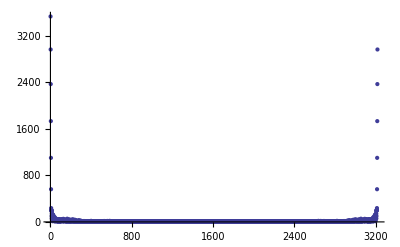

```mathematica
ListPlot[Abs[Fourier[pdata]],PlotRange->All]
```